## Preámbulo

```mathematica
Import[StringJoin[Characters[NotebookFileName[]][[;;-21]]]<>"quantumJA.m"]
```

```mathematica
$memLimit=10*10^9;
$Pre=Function[expr,MemoryConstrained[expr,$memLimit,Print["memory limit exceded"]],{HoldAll}];
```

## Eigenvalores de los canales PCE

### 1 qubit

#### Cálculo analítico de eigenvalores

```mathematica
Subscript[r, 0]=1;eigVal1q=PCE[Table[Subscript[r, i],{i,0,3}]]//Reshuffle//Eigenvalues;eigVal1q
```

{1/4 (1+r_1-r_2-r_3),1/4 (1-r_1-r_2+r_3),1/4 (1-r_1+r_2-r_3),1/4 (1+r_1+r_2+r_3)}

```mathematica
$Assumptions=And@@Table[Subscript[r, i]==1,{i,1,3}];
eigVal1qSigns=(If[FullSimplify[#>0],1,-1]&/@List@@Expand[#])&/@eigVal1q;
eigVal1qSigns//TableForm
$Assumptions=True;
```

1 | 1 | -1 | -1
1 | -1 | -1 | 1
1 | -1 | 1 | -1
1 | 1 | 1 | 1

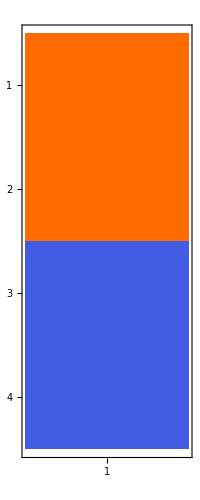
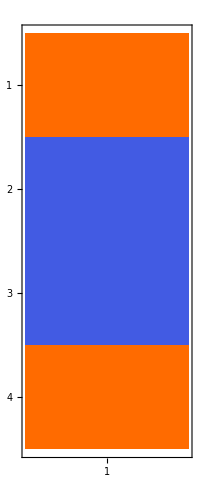
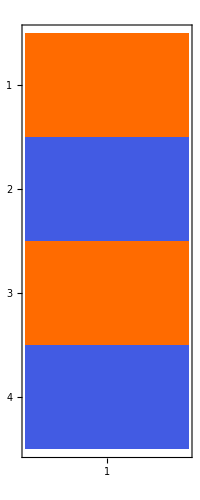
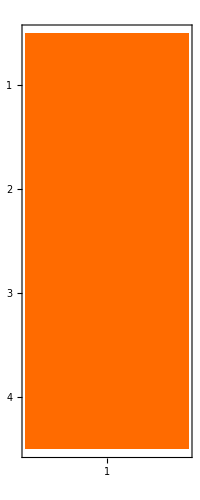

```mathematica
MatrixPlot/@ArrayReshape[eigVal1qSigns,{4,4,1}]
```

### 2 qubits

#### Cálculo analítico de eigenvalores:

```mathematica
Subscript[r, 0,0]=1;eigVal2q=PCE[Table[Subscript[r, i,j],{i,0,3},{j,0,3}]//Flatten]//Reshuffle//Eigenvalues;eigVal2q//TableForm
```

1/16 (1+r_(0,1)+r_(0,2)+r_(0,3)+r_(1,0)+r_(1,1)+r_(1,2)+r_(1,3)-r_(2,0)-r_(2,1)-r_(2,2)-r_(2,3)-r_(3,0)-r_(3,1)-r_(3,2)-r_(3,3))
1/16 (1+r_(0,1)+r_(0,2)+r_(0,3)-r_(1,0)-r_(1,1)-r_(1,2)-r_(1,3)+r_(2,0)+r_(2,1)+r_(2,2)+r_(2,3)-r_(3,0)-r_(3,1)-r_(3,2)-r_(3,3))
1/16 (1+r_(0,1)-r_(0,2)-r_(0,3)+r_(1,0)+r_(1,1)-r_(1,2)-r_(1,3)+r_(2,0)+r_(2,1)-r_(2,2)-r_(2,3)+r_(3,0)+r_(3,1)-r_(3,2)-r_(3,3))
1/16 (1+r_(0,1)-r_(0,2)-r_(0,3)-r_(1,0)-r_(1,1)+r_(1,2)+r_(1,3)-r_(2,0)-r_(2,1)+r_(2,2)+r_(2,3)+r_(3,0)+r_(3,1)-r_(3,2)-r_(3,3))
1/16 (1-r_(0,1)+r_(0,2)-r_(0,3)+r_(1,0)-r_(1,1)+r_(1,2)-r_(1,3)-r_(2,0)+r_(2,1)-r_(2,2)+r_(2,3)-r_(3,0)+r_(3,1)-r_(3,2)+r_(3,3))
1/16 (1-r_(0,1)+r_(0,2)-r_(0,3)-r_(1,0)+r_(1,1)-r_(1,2)+r_(1,3)+r_(2,0)-r_(2,1)+r_(2,2)-r_(2,3)-r_(3,0)+r_(3,1)-r_(3,2)+r_(3,3))
1/16 (1-r_(0,1)-r_(0,2)+r_(0,3)+r_(1,0)-r_(1,1)-r_(1,2)+r_(1,3)+r_(2,0)-r_(2,1)-r_(2,2)+r_(2,3)+r_(3,0)-r_(3,1)-r_(3,2)+r_(3,3))
1/16 (1-r_(0,1)-r_(0,2)+r_(0,3)-r_(1,0)+r_(1,1)+r_(1,2)-r_(1,3)-r_(2,0)+r_(2,1)+r_(2,2)-r_(2,3)+r_(3,0)-r_(3,1)-r_(3,2)+r_(3,3))
1/16 (1-r_(0,1)-r_(0,2)+r_(0,3)-r_(1,0)+r_(1,1)+r_(1,2)-r_(1,3)+r_(2,0)-r_(2,1)-r_(2,2)+r_(2,3)-r_(3,0)+r_(3,1)+r_(3,2)-r_(3,3))
1/16 (1-r_(0,1)-r_(0,2)+r_(0,3)+r_(1,0)-r_(1,1)-r_(1,2)+r_(1,3)-r_(2,0)+r_(2,1)+r_(2,2)-r_(2,3)-r_(3,0)+r_(3,1)+r_(3,2)-r_(3,3))
1/16 (1-r_(0,1)+r_(0,2)-r_(0,3)-r_(1,0)+r_(1,1)-r_(1,2)+r_(1,3)-r_(2,0)+r_(2,1)-r_(2,2)+r_(2,3)+r_(3,0)-r_(3,1)+r_(3,2)-r_(3,3))
1/16 (1-r_(0,1)+r_(0,2)-r_(0,3)+r_(1,0)-r_(1,1)+r_(1,2)-r_(1,3)+r_(2,0)-r_(2,1)+r_(2,2)-r_(2,3)+r_(3,0)-r_(3,1)+r_(3,2)-r_(3,3))
1/16 (1+r_(0,1)-r_(0,2)-r_(0,3)-r_(1,0)-r_(1,1)+r_(1,2)+r_(1,3)+r_(2,0)+r_(2,1)-r_(2,2)-r_(2,3)-r_(3,0)-r_(3,1)+r_(3,2)+r_(3,3))
1/16 (1+r_(0,1)-r_(0,2)-r_(0,3)+r_(1,0)+r_(1,1)-r_(1,2)-r_(1,3)-r_(2,0)-r_(2,1)+r_(2,2)+r_(2,3)-r_(3,0)-r_(3,1)+r_(3,2)+r_(3,3))
1/16 (1+r_(0,1)+r_(0,2)+r_(0,3)-r_(1,0)-r_(1,1)-r_(1,2)-r_(1,3)-r_(2,0)-r_(2,1)-r_(2,2)-r_(2,3)+r_(3,0)+r_(3,1)+r_(3,2)+r_(3,3))
1/16 (1+r_(0,1)+r_(0,2)+r_(0,3)+r_(1,0)+r_(1,1)+r_(1,2)+r_(1,3)+r_(2,0)+r_(2,1)+r_(2,2)+r_(2,3)+r_(3,0)+r_(3,1)+r_(3,2)+r_(3,3))

#### Construcción de los eigenvalores a partir de los eigenvalores de 1 qubit:

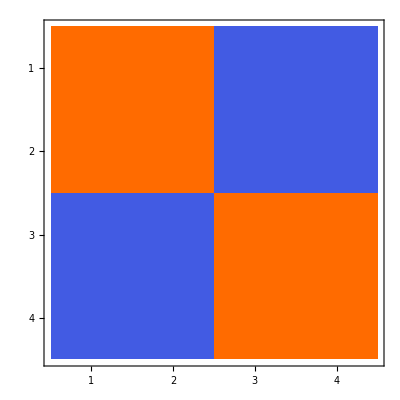
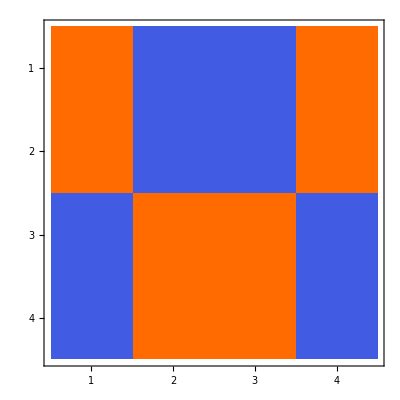
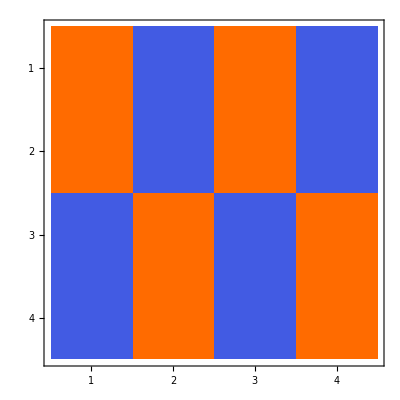
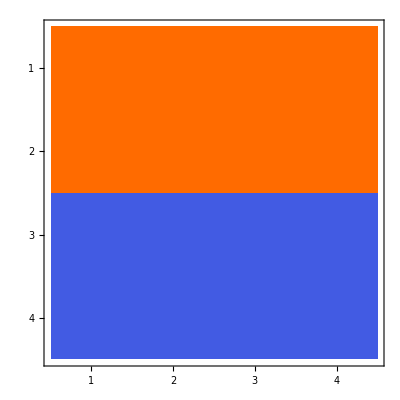
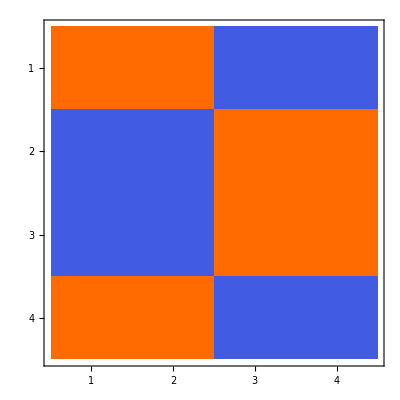
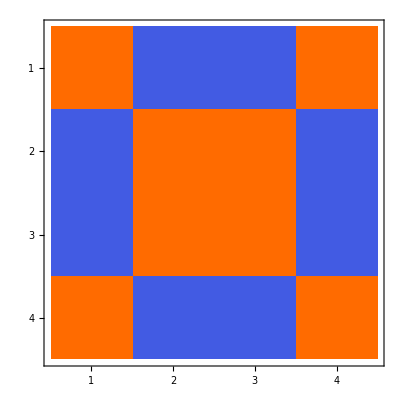
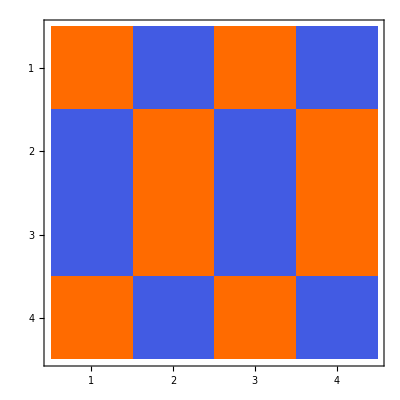
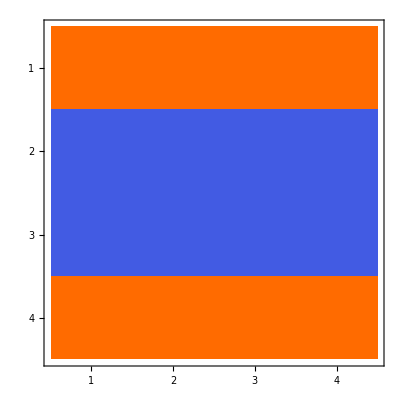

```mathematica
MatrixPlot/@Flatten[Table[KroneckerProduct[eigVal1qSigns[[i]],eigVal1qSigns[[j]]],{i,1,4},{j,1,4}],1]
```

## Viendo qué pedo

```mathematica
eigVal1qSigns//MatrixForm
```

(1 | 1 | -1 | -1
1 | -1 | -1 | 1
1 | -1 | 1 | -1
1 | 1 | 1 | 1)

```mathematica
matrix1q=ReplacePart[eigVal1qSigns,Position[eigVal1qSigns,-1]->0]
```

{{1,1,0,0},{1,0,0,1},{1,0,1,0},{1,1,1,1}}

```mathematica
Transpose[matrix1q[[;;3,2;;]]]//MatrixForm
```

(1 | 0 | 0
0 | 0 | 1
0 | 1 | 0)

```mathematica
Inverse[Transpose[matrix1q[[;;3,2;;]]]].eigVal1qSigns[[;;3,2;;]].Transpose[matrix1q[[;;3,2;;]]]//MatrixForm
```

(1 | -1 | -1
-1 | -1 | 1
-1 | 1 | -1)

```mathematica
1/2(eigVal1qSigns.#&/@matrix1q)
```

{{1,0,0,1},{0,1,0,1},{0,0,1,1},{0,0,0,2}}

```mathematica
Matrix=ReplacePart[eigMatrix,Position[eigMatrix,-1]->0]
```

{{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
eigMatrix=ArrayReshape[Flatten[Table[KroneckerProduct[eigVal1qSigns[[i]],eigVal1qSigns[[j]]],{i,1,4},{j,1,4}],1],{16,16}];
```

```mathematica
eigMatrix[[;;15,2;;]]//MatrixForm
```

(1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
-1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
-1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1
-1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
-1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
-1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
-1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1)

```mathematica
resultingMatrix=(eigMatrix.#&/@Matrix);resultingMatrix//MatrixForm
```

(8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16)

```mathematica
Matrix//MatrixForm
```

(1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
#.eigMatrix.#&/@Matrix
```

{16,0,16,8,0,16,0,8,16,0,16,8,8,8,8,16}

```mathematica
Inverse[eigMatrix[[;;15,2;;]]].resultingMatrix.eigMatrix[[;;15,2;;]]//MatrixForm
```

(8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8)

```mathematica
AllTrue[ArrayReshape[Flatten[Table[KroneckerProduct[eigVal1qSigns[[i]],eigVal1qSigns[[j]]],{i,1,4},{j,1,4}],1],{16,16}].#,#≥0&]&/@Matrix
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Matrix
```

{{1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{0,0,1,0,1,1,0,0,1,1,0,1,0,0,1},{0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}}

```mathematica
Count[#,1]&/@Transpose[ArrayReshape[Flatten[Table[KroneckerProduct[eigVal1qSigns[[i]],eigVal1qSigns[[j]]],{i,1,4},{j,1,4}],1],{16,16}]]
```

{16,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Clear[a];{{a,b,c},{d,e,f},{g,h,i}}.{a,b,c}
```

{a^2+b^2+c^2,a d+b e+c f,a g+b h+c i}

### 3 qubits

#### Construcción de los eigenvalores a partir de los eigenvalores de 1 qubit :

```mathematica
Cube3q[#//Flatten]&/@EigenvalSignsPCE[3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Alejo tiene una explicación analítica de la construcción de los eigenvalores para n qubits :D

## Los eigenvalores pueden definir ‘borrados’ (resultados 2, 3 y 4 qubits)

#### Two next functions need each other. **HW: add this functions to quantumJA.m

```mathematica
EigenvalSignsPCE[qubits_Integer]:=Module[{ind,eigVal1qSigns},
eigVal1qSigns[{1}]=eigVal1qSigns[1]={1,1,1,1};
eigVal1qSigns[{2}]=eigVal1qSigns[2]={1,1,-1,-1};
eigVal1qSigns[{3}]=eigVal1qSigns[3]={1,-1,1,-1};
eigVal1qSigns[{4}]=eigVal1qSigns[4]={1,-1,-1,1};
ind=Tuples[{1,2,3,4},qubits];
If[qubits==1,
{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}},
ArrayReshape[KroneckerProduct@@(eigVal1qSigns/@#)&/@ind,{4^qubits}~Join~ConstantArray[4,qubits]]
]
]
```

```mathematica
NewErase[PCEfrom_,invariantComponents_Integer]:=Module[{qubits},
qubits=Length[Dimensions[PCEfrom][[2;;]]];
DeleteDuplicates[
Flatten[
Table[
DeleteDuplicates[
If[Count[Flatten[#],1]==invariantComponents,#,Nothing]&/@(ReplacePart[PCEfrom[[i]],Position[#,-1]->0]&/@EigenvalSignsPCE[qubits][[;;4^qubits-1]])
]
,{i,Length[PCEfrom]}]
,1]
]
]
```

### 2 qubits

#### **ARREGLAR: no sirve que estas mierdas tomen el último elemento, por si se traba

1

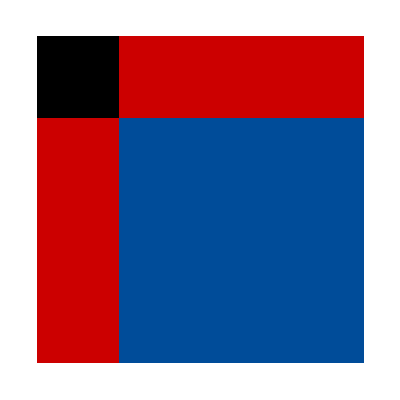

```mathematica
twoQubits={};AppendTo[twoQubits,{ConstantArray[1,{4,4}]}];twoQubits[[1]]//Length
TwoQBoard/@twoQubits[[1]]
```

```mathematica
components=8;
AppendTo[twoQubits,NewErase[twoQubits[[-1]],components]];twoQubits[[-1]]//Length
TwoQBoard/@twoQubits[[-1]]
```

15

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
twoQ=ToExpression[twoQ]
```

{{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,0,0}},{{1,0,1,0},{1,0,1,0},{1,0,1,0},{1,0,1,0}},{{1,0,0,1},{1,0,0,1},{1,0,0,1},{1,0,0,1}},{{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}},{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{{1,0,1,0},{1,0,1,0},{0,1,0,1},{0,1,0,1}},{{1,0,0,1},{1,0,0,1},{0,1,1,0},{0,1,1,0}},{{1,1,1,1},{0,0,0,0},{1,1,1,1},{0,0,0,0}},{{1,1,0,0},{0,0,1,1},{1,1,0,0},{0,0,1,1}},{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},{{1,0,0,1},{0,1,1,0},{1,0,0,1},{0,1,1,0}},{{1,1,1,1},{0,0,0,0},{0,0,0,0},{1,1,1,1}},{{1,1,0,0},{0,0,1,1},{0,0,1,1},{1,1,0,0}},{{1,0,1,0},{0,1,0,1},{0,1,0,1},{1,0,1,0}},{{1,0,0,1},{0,1,1,0},{0,1,1,0},{1,0,0,1}}}

```mathematica
(DiagonalMatrix[#//Flatten].(twoQ[[2]]//Flatten))&/@twoQ
```

{{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0},{1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0},{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0},{1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0},{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0},{1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0},{1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0}}

```mathematica
1/2(ArrayReshape[EigenvalSignsPCE[2][[;;15]],{16-1,16}]+ConstantArray[1,{16-1,16}])//Dimensions
```

{15,16}

```mathematica
{1,1,1,1}.{1,0,0,1}
```

2

```mathematica
FindPCEv2[{ConstantArray[1,16]},8]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
FindPCE[PCEfrom_,components_]:=Module[{qubits,cumulative,canonical,temporal,rows},
qubits=Log[4,Dimensions[PCEfrom][[2]]];
rows=4^qubits-1;
canonical=1/2(ArrayReshape[EigenvalSignsPCE[qubits][[;;rows]],{rows,rows+1}]+ConstantArray[1,{rows,rows+1}]);
cumulative={};
Do[
temporal=DeleteDuplicates[MapThread[Times,{#,PCEfrom[[i]]}]&/@canonical];
cumulative=DeleteDuplicates[cumulative~Join~temporal];
,{i,Length[PCEfrom]}];
cumulative=If[Count[#,1]==components,#,Nothing]&/@cumulative
]
```

```mathematica
FindPCEv2[PCEfrom_,components_]:=Module[{qubits,cumulative,canonical,temporal,rows},
qubits=Log[4,Dimensions[PCEfrom][[2]]];
rows=4^qubits-1;
canonical=1/2(ArrayReshape[EigenvalSignsPCE[qubits][[;;rows]],{rows,rows+1}]+ConstantArray[1,{rows,rows+1}]);
cumulative={};
Do[
Print[PCEfrom[[i]].#==components&/@canonical];
temporal=DeleteDuplicates[(If[PCEfrom[[i]].#==components,PCEfrom[[i]],Nothing])&/@canonical];
cumulative=DeleteDuplicates[cumulative~Join~temporal];
,{i,Length[PCEfrom]}];
cumulative
]
```

```mathematica
q2c8= FindPCE[{ConstantArray[1,16]},8];q2c8//Length
```

15

```mathematica
q2c4= FindPCE[q2c8,4];q2c4//Length
```

35

```mathematica
q2c2= FindPCE[q2c4,2];q2c2//Length
```

15

```mathematica
q2c1= FindPCE[q2c2,1];q2c1//Length
```

1

```mathematica
q3c64={ConstantArray[1,64]};
```

```mathematica
q3c32= FindPCE[q3c64,32];q3c32//Length
```

63

```mathematica
AbsoluteTiming[q3c16= FindPCE[q3c32,16];]
q3c16//Length
```

{0.081714,Null}

651

```mathematica
AbsoluteTiming[FindPCEv2[q3c32,16];]
```

{0.018681,Null}

```mathematica
AbsoluteTiming[q3c8= FindPCE[q3c16,8];]
q3c8//Length
```

{1.28565,Null}

1395

```mathematica
AbsoluteTiming[ FindPCEv2[q3c16,8];]
```

{0.171632,Null}

```mathematica
AbsoluteTiming[q3c4= FindPCE[q3c8,4];]
q3c4//Length
```

{2.5668,Null}

651

```mathematica
AbsoluteTiming[ FindPCEv2[q3c8,4];]
```

{0.344803,Null}

```mathematica
q3c2= FindPCE[q3c4,2];q3c2//Length
```

63

```mathematica
q3c1= FindPCE[q3c2,1];q3c1//Length
```

1

```mathematica
q4c256={ConstantArray[1,256]};
```

```mathematica
AbsoluteTiming[q4c128= FindPCE[q4c256,128];]
q4c128//Length
```

{0.026586,Null}

255

```mathematica
AbsoluteTiming[q4c64= FindPCE[q4c128,64];]
q4c64//Length
```

{9.91793,Null}

10795

```mathematica
AbsoluteTiming[q4c32= FindPCE[q4c64,32];]
q4c32//Length
```

{4718.53,Null}

97155

```mathematica
AbsoluteTiming[q4c16= FindPCE[q4c32,16];]
q4c16//Length
```

$Aborted

0

```mathematica
q4c128v2= FindPCE[q4c256,128];q4c128v2//Length
```

255

```mathematica
q4c64v2= FindPCEv2[q4c128v2,64];q4c64v2//Length
```

0

```mathematica
components=4;
AppendTo[twoQubits,NewErase[twoQubits[[-1]],components]];twoQubits[[-1]]//Length
TwoQBoard/@twoQubits[[-1]]
```

35

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
components=2;
AppendTo[twoQubits,NewErase[twoQubits[[-1]],components]];twoQubits[[-1]]//Length
TwoQBoard/@twoQubits[[-1]]
```

15

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
components=1;
AppendTo[twoQubits,NewErase[twoQubits[[-1]],components]];twoQubits[[-1]]//Length
TwoQBoard/@twoQubits[[-1]]
```

1

{-Graphics-}

```mathematica
Reverse[Length[#]&/@twoQubits]
```

{1,15,35,15,1}

### 3 qubits

```mathematica
threQubits={};AppendTo[threQubits,{ConstantArray[1,{4,4,4}]}];threQubits[[1]]//Length
Cube3q[#//Flatten]&/@threQubits[[1]]
```

1

{-Graphics3D-}

```mathematica
SeedRandom[1354948];components=32;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@(threQubits[[-1,#]]&/@RandomInteger[{1,Length[threQubits[[-1]]]},9])
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SeedRandom[1354948];components=16;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@(threQubits[[-1,#]]&/@RandomInteger[{1,Length[threQubits[[-1]]]},9])
```

651

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SeedRandom[1354948];components=8;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@(threQubits[[-1,#]]&/@RandomInteger[{1,Length[threQubits[[-1]]]},9])
```

1395

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SeedRandom[1354948];components=4;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@(threQubits[[-1,#]]&/@RandomInteger[{1,Length[threQubits[[-1]]]},9])
```

651

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SeedRandom[1354948];components=2;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@(threQubits[[-1,#]]&/@RandomInteger[{1,Length[threQubits[[-1]]]},9])
```

63

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SeedRandom[1354948];components=1;
AppendTo[threQubits,NewErase[threQubits[[-1]],components]];threQubits[[-1]]//Length
Cube3q[#//Flatten]&/@threQubits[[-1]]
```

1

{-Graphics3D-}

```mathematica
Reverse[Length[#]&/@threQubits]
```

{1,63,651,1395,651,63,1}

### 4 qubits

```mathematica
fourQubits={};AppendTo[fourQubits,{ConstantArray[1,{4,4,4,4}]}];fourQubits[[1]]//Length
```

1

```mathematica
SeedRandom[1354948];components=128;
AppendTo[fourQubits,NewErase[fourQubits[[-1]],components]];fourQubits[[-1]]//Length
```

255

```mathematica
SeedRandom[1354948];components=64;
AppendTo[fourQubits,NewErase[fourQubits[[-1]],components]];fourQubits[[-1]]//Length
```

10795

```mathematica
SeedRandom[1354948];components=32;
AppendTo[fourQubits,NewErase[fourQubits[[-1]],components]];fourQubits[[-1]]//Length
```

97155

```mathematica
SeedRandom[1354948];components=16;
AppendTo[fourQubits,NewErase[fourQubits[[-1]],components]];fourQubits[[-1]]//Length
```

```mathematica
Reverse[Length[#]&/@fourQubits]
```

{97155,10795,255,1}

## Una explicación física a los borrados. Una caracterización general de los canales PCE????

## Otros

```mathematica
NewErase2[PCEfrom_,invariantComponents_Integer]:=Module[{qubits,iteration,goodOnes},
qubits=Length[Dimensions[PCEfrom][[2;;]]];
goodOnes={};
Do[
iteration=DeleteDuplicates[If[Count[Flatten[#],1]==invariantComponents,#,Nothing]&/@(ReplacePart[PCEfrom[[i]],Position[#,-1]->0]&/@EigenvalSignsPCE[qubits][[;;4^qubits-1]])];
goodOnes=DeleteDuplicates[Join[goodOnes,iteration]];
,{i,Length[PCEfrom]}];
goodOnes
]
```

```mathematica
q4c16=NewErase2[fourQubits[[4]],16];q4c16//Length
```

$Aborted